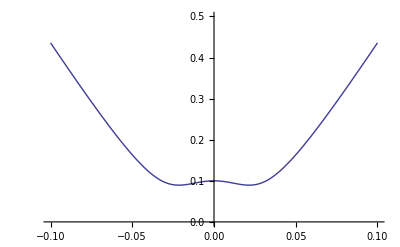

```mathematica
d=0.12; t=0.4; c=6.25;a1=0.016; G1=0.00086; b=0.0004138; mu1=0.13;
f4[x_,n1_,U_]:=√(U^2+(a1*n1/x)+t^2/2-√((t^2+4*U^2)*(a1*n1/x)+t^4/4));
f4[0.1,1,0.1];
F2[x_,n1_,U_]=(1/((mu1-f4[x,n1,U])^2+G1^2));
F1[x_,U_]=b*G1*Sum[F2[x,n1,U],{n1,0,100}]*(1/x);
f144[x_,U_]:=√(U^2+(6.25*x)^2+t^2*0.5-√((t^2+4*U^2)*(6.25*x)^2+t^4/4));
Plot[f144[x,0.1],{x,-0.1,0.1},PlotRange->{0,0.5}]
```

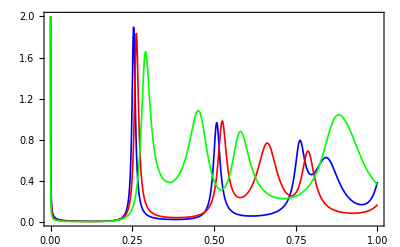

```mathematica
Plot[{F1[x,0.155],F1[x,0.160],F1[x,0.168]},{x,0,1},PlotRange->{0,2},PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Red},{Thickness[0.003],Green}},Frame->True]
```

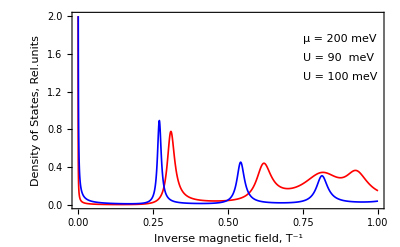

```mathematica
d=0.12; mu2=0.2;
f5[x_,n1_,U_]:=√(d^2+U^2+(a1*n1/x)+t^2/2-√((t^2+4*U^2)*(a1*n1/x)+4*U^2*d^2+2*t^2*d*U+t^4/4));
F3[x_,n1_,U_]=(1/((mu2-f5[x,n1,U])^2+G1^2));
F4[x_,U_]=b*0.5*G1*Sum[F3[x,n1,U],{n1,0,100}]*(1/x);
Plot[{F4[x,-0.1],F4[x,-0.09]},{x,0,1},PlotRange->{0,2},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Blue}},FrameLabel->{Style["Inverse magnetic field, T^-1",10],Style["Density of States, Rel.units",10]},Epilog->{{Black,Text["μ = 200 meV",{0.75,1.7},{-1,-1}]},{Black,Text["U = 90  meV",{0.75,1.5},{-1,-1}]},{Black,Text["U = 100 meV",{0.75,1.3},{-1,-1}]}},Frame->True]
```

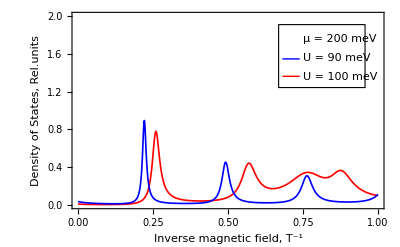

```mathematica
d=0.12; mu3=0.2;
f6[x_,n1_,U_]:=√(d^2+U^2+(a1*n1/x)+t^2-2*√((t^2+U^2)*(a1*n1/x)+U^2*d^2));
F5[x_,n1_,U_]=(1/((mu3-f6[x,n1,U])^2+G1^2));
F6[x_,U_]=b*0.4*G1*Sum[F5[x,n1,U],{n1,0,100}]*(1/x);
Plot[{F6[x+0.05,-0.1],F4[x+0.05,-0.10]},{x,0,1},PlotRange->{0,2},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Blue}},FrameLabel->{Style["Inverse magnetic field, T^-1",10],Style["Density of States, Rel.units",10]},Epilog->{{Black,Text["μ = 200 meV",{0.75,1.7},{-1,-1}]},{Black,Text["U = 100 meV",{0.75,1.5},{-1,-1}]},{Black,Text["Γ = 10 K",{0.75,1.3},{-1,-1}]}},Frame->True]
```

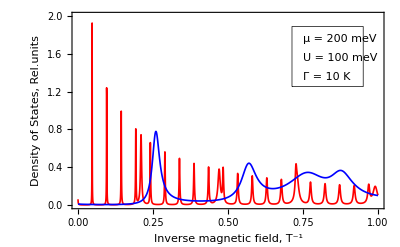

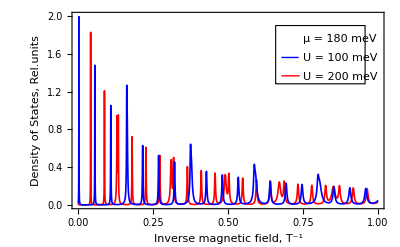

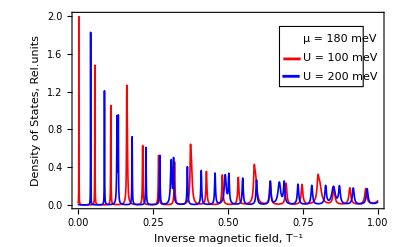

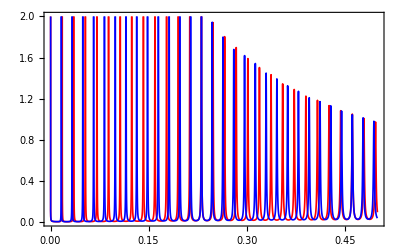

```mathematica
F9[x_,n1_,U_]=(1/((0.55-f6[x,n1,U])^2+G1^2));
F16[x_,U_]=b*G1*Sum[F9[x,n1,U],{n1,0,100}]*(1/x);
Plot[{F16[x,-0.1],F16[x,-0.2]},{x,0,0.5},PlotRange->{0,2},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Blue}},Frame->True]
```